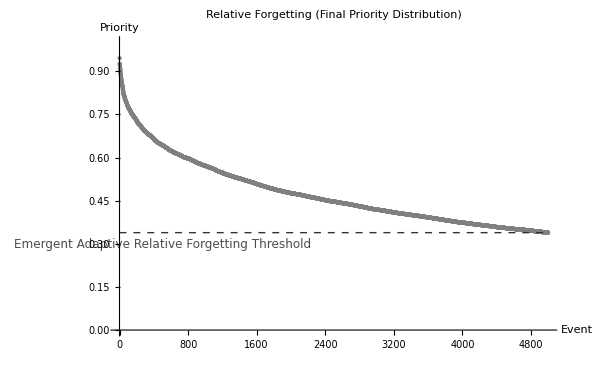

```mathematica
(* Define constants *)
	λ=0.25; (* Decay constant *)
	timeDuration=50; (* Total time duration *)
	numInitialEvents=200; (* Initial number of events *)
	queueCapacity=5000; (* Capacity of the priority queue *)
	newEventsPerStep=500; (* Number of new events introduced per time step *)
	
	(* Generate initial truth values and neuron activations for events *)
	RandomSeed[123];
	truthValues=RandomReal[{0,1},numInitialEvents];
	neuronActivations=RandomReal[{0,1},numInitialEvents];
	
	(* Define expectation and priority functions *)
	expectation[f_]:=0.5*(1-f)+0.5;
	priority[f_,activation_]:=expectation[f]*activation;
	
	(* Calculate initial priorities *)
	initialPriorities=Table[priority[truthValues[[i]],neuronActivations[[i]]],{i,numInitialEvents}];
	
	(* Simulate priority decay over time *)
	decayFunction[p_,t_]:=p*Exp[-λ*t];
	timeSteps=Range[0,timeDuration,0.1];
	
	(* Priority queue simulation with continuous event flow *)
	finalQueueState=Module[
	  {queue,eventPriority,newTruthValues,newNeuronActivations,newPriorities},
	  queue=initialPriorities;
	  Do[
	   (* Decay priorities at each time step *)
	   queue=decayFunction[queue,0.1];
	
	   (* Introduce new events at each time step *)
	   newTruthValues=RandomReal[{0,1},newEventsPerStep];
	   newNeuronActivations=RandomReal[{0,1},newEventsPerStep];
	   newPriorities=Table[priority[newTruthValues[[j]],newNeuronActivations[[j]]],{j,newEventsPerStep}];
	
	   (* Add new events to the queue and maintain capacity *)
	   queue=SortBy[Join[queue,newPriorities],-# &];
	   If[Length[queue]>queueCapacity,queue=Take[queue,queueCapacity]];
	   ,
	   {i,Length[timeSteps]}
	   ];
	  queue
	];
	
	(* Determine the threshold for the lowest priority in the queue *)
	lowestPriorityThreshold=Min[finalQueueState];
	
	(* Plot the final state of the queue in grayscale with threshold line and label *)
	ListPlot[finalQueueState,PlotRange->{{0,queueCapacity},{0,1}},
	 PlotStyle->{PointSize[Small],GrayLevel[0.5]},
	 PlotLabel->"Relative Forgetting (Final Priority Distribution)",
	 AxesLabel->{"Event","Priority"},
	 LabelStyle->{FontSize->14},
	 Epilog->{
	   GrayLevel[0.2],Dashed,Thick,Line[{{0,lowestPriorityThreshold},{queueCapacity,lowestPriorityThreshold}}],
	   Text[Style["Emergent Adaptive Relative Forgetting Threshold",GrayLevel[0.3],FontSize->12],
	    {500,lowestPriorityThreshold-0.04},{-1,0}]
	  }
	]
```